```mathematica
(*Task 1*)
(*1*)
f[x_]=5 Cos[x]^2;
Subscript[x, 0]=0;
Subscript[x, 1]=π/6;
Subscript[x, 2]=π/4;
Subscript[x, 3]=π/3;
Subscript[x, 4]=π/2;
Subscript[x, 5]=π;
Subscript[x, 6]=9π/5;
Subscript[x, 7]= π/7;
NN=7;
n=(NN-1)/2;
Subscript[T, n][x_]=Subscript[a, 0]+∑_(k=1)^n (Subscript[a, k] Sin[k x] + Subscript[b, k] Cos[k x])
eqv=Table[Subscript[T, n][Subscript[x, j]] == f[Subscript[x, j]], {j, 0, NN-1}];
Koef=Solve[Eqv, {}] //Flatten //N
Subscript[T, n][x_]=Subscript[T, n][x] //.Koef
```

(9.83214×10^-13)_0+Sin[x] (9.83214×10^-13)_1+Sin[2 x] (9.83214×10^-13)_2+Sin[3 x] (9.83214×10^-13)_3+Cos[x] (2.42247×10^-11)_1+Cos[2 x] (2.42247×10^-11)_2+Cos[3 x] (2.42247×10^-11)_3

{(9.83214×10^-13)_0→2.5,(9.83214×10^-13)_1→0.,(9.83214×10^-13)_2→0.,(9.83214×10^-13)_3→0.,(2.42247×10^-11)_1→0.,(2.42247×10^-11)_2→2.5,(2.42247×10^-11)_3→0.}

2.5+2.5 Cos[2 x]

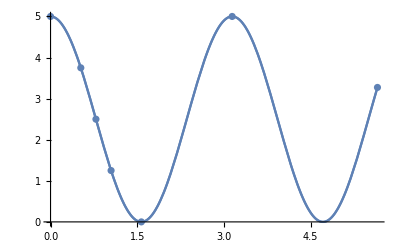

```mathematica
(*2*)
Gr1=ListPlot[Table[{Subscript[x, i], Subscript[T, n][Subscript[x, i]]}, {i, 0, NN-1}]];
Gr2=Plot[Subscript[T, n][x], {x,Subscript[x, 0], Subscript[x, 6]}];
Gr3=Plot[f[x], {x, Subscript[x, 0], Subscript[x, 6]}];
Show[Gr1, Gr2, Gr3]
```

```mathematica
(*3*)
approximate=Subscript[T, n][Subscript[x, 7]]
accurate=f[Subscript[x, 7]]//N
a=Abs[accurate-approximate]
b=a/approximate*100//Abs
```

4.05872

4.05872

9.83214×10^-13

2.42247×10^-11

```mathematica
(*Task 2*)
```

```mathematica
X={0.1,0.2,0.3,0.4}; 
F={1.87,2.054,5.909,8.872};
n = Length[X]-1;
Do [{Subscript[x, i]= X[[i+1]], Subscript[f, i] = F[[i+1]]}, {i, 0, n}]
eqv:= Table[∑_(i=0)^n Subscript[A, i] Subscript[x, i]^j  ==D[y^j, {y, m}]/.y-> xx, {j, 0, n}]
Koef:=Solve[eqv, {}]//Flatten
P:=∑_(i=0)^n Subscript[A, i] Subscript[f, i]/.Koef
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}]
L=InterpolatingPolynomial[Tbl,t];
P1:= D[L, {t,m}]/.t-> xx
m=1; xx= 0.1; {P, P1, P==P1}
m=1; xx= 0.2; {P, P1, P==P1}
m=2; xx=0; {P, P1, P==P1}
m=3; xx=0.5;{P, P1, P==P1}
```

{{0.1,1.87},{0.2,2.054},{0.3,5.909},{0.4,8.872}}

{-31.725,-31.725,True}

{27.8,27.8,True}

{1279.7,1279.7,True}

{-4563.,-4563.,True}

```mathematica
w[x_]=∏_(i=0)^n (x-Subscript[x, i]);
m=1; xx= 0.1; 
(M*D[w[x],{x,m}]/.x->xx)/((n+1)!)//Abs
```

0.00025 Abs[M]

```mathematica
m=1; xx= 0.2;
(M*D[w[x],{x,m}]/.x->xx)/((n+1)!)//Abs
```

0.0000833333 Abs[M]

```mathematica
m=2; xx=0;
(M*D[w[x],{x,m}]/.x->xx)/((n+1)!)//Abs
```

0.0291667 Abs[M]

```mathematica
m=3; xx=0.5; 
(M*D[w[x],{x,m}]/.x->xx)/((n+1)!)//Abs
```

0.25 Abs[M]